## Eq.(134)-Eq.(138)

```mathematica
assumptions={τ<0,k>0,m>0,H>0};
```

#### 其实更正规的写法应该是z=-k τ，这样更加正规，这里的τ被认为大于0.

```mathematica
DSolve[X''[τ]+(k^2+1/τ^2(m^2/H^2-2))X[τ]==0,X[τ],τ]
```

{{X[τ]→√τ BesselJ[1/2 √(9-(4 m^2)/H^2),k τ] C[1]+√τ BesselY[1/2 √(9-(4 m^2)/H^2),k τ] C[2]}}

#### Hankle 和Bessel的变换， -Graphics- 再重新定义c1，c2即可得到（136）下面的式子

### Hankle的展开

```mathematica
ν=1/2 √(9-(4 m^2)/H^2);
```

```mathematica
Series[HankelH1[ν1,x],{x,∞,1}]//Normal//FullSimplify
```

((1-ⅈ) ⅇ^(ⅈ x-(ⅈ π ν1)/2))/(√π √x)

```mathematica
√2 ⅇ^(ⅈ x-(ⅈ π ν1)/2-(I π)/4)/(√π √x)-((1-ⅈ) ⅇ^(ⅈ x-(ⅈ π ν1)/2))/(√π √x)//FullSimplify
```

0

```mathematica
Series[HankelH2[ν1,x],{x,∞,1}]//Normal//FullSimplify
```

((1+ⅈ) ⅇ^(1/2 ⅈ (-2 x+π ν1)))/(√π √x)

```mathematica
Series[HankelH1[ν1,x],{x,0,1}]//Normal//FullSimplify
```

-(ⅈ 2^ν1 x^-ν1 Gamma[ν1])/π+(2^-ν1 x^ν1 (1+ⅈ Cot[π ν1]))/Gamma[1+ν1]

#### 第一个是冻结模，第二个是衰减模，保留第一个。

```mathematica
√(2/π)Exp[-I π/2] 2^(ν1-3/2)Gamma[ν1]/Gamma[3/2] x^-ν1
```

-(ⅈ 2^ν1 x^-ν1 Gamma[ν1])/π

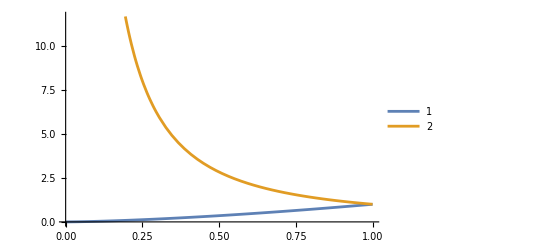

```mathematica
Plot[{x^(3/2),x^(-3/2)},{x,0,1},PlotLegends->{"1","2"}]
```